## Section | Characteristic Functions and Phase Space Representations

#### Paclet loading

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Introduction to Characteristic Functions

If we have a probability density p(x) associated with a random variable X, it should be the case that p(x) >= 0   ∀ x ∈ ℝ and ∫ p(x) ⅆx=1 . The nth moment of the probability density is   ,  the function p(x)  can be determined if information of  all the moments is known.

Because we can define a characteristic function

so they are related by a Fourier transform

Three characteristic functions are important in quantum optics:

related by  C_W(λ) = C_N(λ)ⅇ^(-1/2 |λ|^2)=C_A(λ)ⅇ^(1/2 |λ|^2)
There is also a general parametrized characteristic function:

with C(λ,0) = C_W(λ), C(λ,1) = C_N(λ) and C(λ, -1) = C_A(λ)

### Relation between characteristic functions and quasi-probability distributions

The characteristic functions are related to quasi-probability distributions , they can be related via the Fourier transform of the characteristic functions

Wigner:

Husimi-Q function:

Glauber-Sudarshan P-function:

S-parameter quasi-probability function:

The s-parameter quasi-probability function can generate the other ones picking certain values of s.

Computationally these functions can be demanding to calculate for an arbitrary state or density matrix . There are good numerical techniques to compute the Wigner and Husimi Q-function , but not for the Glauber P-because it is highly singular in general.

The Husimi function is always positive, unlike the Wigner and P-function that can take negative values in some region that  indicate nonclassical behavior, however the converse is not a true a state can be nonclassical and still have positive Wigner function.

The P-function is a good theoretical tool but can be impractical in many cases, this is why the preferred of all three is the Wigner because it can also show quantum nature of nonclassical states (unlike Husimi).

### Wigner function

In terms of wave functions the Wigner function can be calculated as:

Other way of calculating the Wigner function for a density operator ρ is:

with

The Wigner function is normalized in phase space, this means the integral over all phase space is equal to 1 (this also holds for Husimi-Q and Glauber-Sudarshan):

The Wigner function also has other important property, integrating over one of the variables (a marginal) reflects a probability density consistent with quantum measurement theory (this does not hold for Husimi-Q and Glauber-Sudarshan)

Position distribution:

Momentum distribution:

Operator expectation values are calculated as phase space averages of the Wigner function, say for an operator F̂ that is a function of the operators x̂ and p̂:

In the Quantum Framework, we can use WignerRepresentation:

Define the superposition state 1/(√2)( |0⟩ + |1⟩):

```mathematica
ψ = QuantumState["+",$FockSize]
```

1/(√2)0+1/(√2)1

Get the function that represents the phase space representation in the selected rectangular spatial domain:

```mathematica
wig = WignerRepresentation[ψ,{-4,4},{-4,4}]
```

InterpolatingFunction[…]

Plot the function:

```mathematica
Plot3D[wig[x,p],{x,-4,4},{p,-4,4},]
```

-Graphics3D-

Normalization condition:

```mathematica
Integrate[wig[x,p],{x,-4,4},{p,-4,4}]
```

0.999999

Integrating along one variable to get marginals:

```mathematica
posMarginal =Integrate[wig[x,p],{p,-4,4}];
momenMarginal =Integrate[wig[x,p],{x,-4,4}];
```

Position marginal:

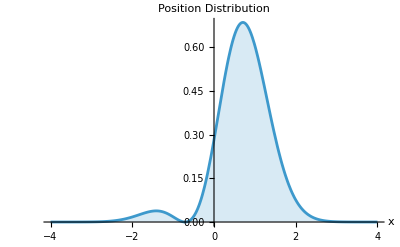

```mathematica
Plot[posMarginal,{x,-4,4},Filling->Bottom,AxesLabel->{"x", "Position Distribution"}]
```

Momentum marginal:

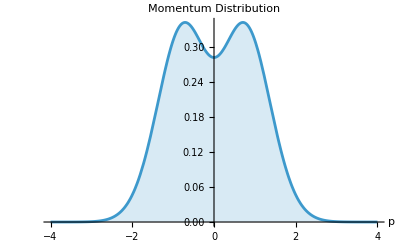

```mathematica
Plot[momenMarginal,{p,-4,4},Filling->Bottom,AxesLabel->{"p", "Momentum Distribution"}]
```

Average position:

```mathematica
NIntegrate[x posMarginal,{x,-4,4}]
```

0.707106

Average momentum:

```mathematica
NIntegrate[p momenMarginal,{p,-4,4},Method->"LocalAdaptive"]
```

2.62193×10^-17

Explicit calculation of averages with the brackets of the quadrature operators:

```mathematica
(SuperDagger[ψ]@(√2#)@ψ)["Scalar"]& /@QuadratureOperators[]
```

{1/(√2),0}

The trace definition can be rewritten in terms of a kernel 𝒦

Matrix elements of the 𝒦 kernel:

```mathematica
𝒦mn[γ_,{m_,n_}]:=With[{ζ=2γ},(-1)^n Exp[-Abs[ζ]^2/2]If[m>=n,√((n!)/(m!))ζ^(m-n)LaguerreL[n,m-n,Abs[ζ]^2],√((m!)/(n!))Conjugate[-ζ]^(n-m)LaguerreL[m,n-m,Abs[ζ]^2]]]
```

We can define a simple function for calculating the Wigner function as a trace, summing  the non-zero values  ∑_mn  ρ_(m n) 𝒦_(n m):

```mathematica
wignerTrace[ρ_SparseArray, α_]:= With[{pos = ρ["ExplicitPositions"], vals= ρ["ExplicitValues"]}, 2/π Dot[vals, 𝒦mn[α, {#2-1,#1-1}]& @@@ pos]]
```

Get the density matrix of the state:

```mathematica
ρ = ψ["DensityMatrix"];
```

Use the trace based definition to get a symbolic function:

```mathematica
func = ComplexExpand[wignerTrace[ρ,α]/. α->(x+ⅈ p)/(√2)]
```

(2 ⅇ^(-p^2-x^2) p^2)/π+(2 √2 ⅇ^(-p^2-x^2) x)/π+(2 ⅇ^(-p^2-x^2) x^2)/π

Plot the function, of course we get the same result as before:

```mathematica
Plot3D[1/2func,{x,-4,4},{p,-4,4},]
```

-Graphics3D-

Integral over all phase space, we include a 1/2 factor due to how the differentials of α and x and p relate (α = (x + ⅈ p)/√2):

```mathematica
Integrate[1/2func,{x,-∞,∞},{p,-∞,∞}]
```

1

Symbolic marginal of x:

```mathematica
xmarginal =Integrate[1/2func,{p,-∞,∞}]
```

(ⅇ^(-x^2) (1+2 x (√2+x)))/(2 √π)

Symbolic marginal of p:

```mathematica
pmarginal = Integrate[1/2func,{x,-∞,∞}]
```

(ⅇ^(-p^2) (1+2 p^2))/(2 √π)

Plotting the marginals:

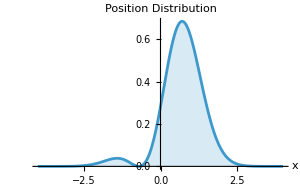

```mathematica
Plot[xmarginal,{x,-4,4},PlotRange->All,AxesLabel->{"x", "Position Distribution"},Filling->Bottom]
```

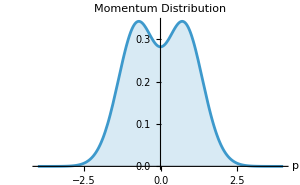

```mathematica
Plot[pmarginal,{p,-4,4},PlotRange->All,AxesLabel->{"p", "Momentum Distribution"},Filling->Bottom]
```

Let’s calculate the Wigner function for the Fock states |0⟩, |2⟩, |5⟩ and a coherent state |α⟩. Fock states |n⟩(n>1) have negative values in their Wigner function showing they are non-classical. In phase space, the vacuum and any coherent state have a gaussian distribution ,the value of α indicates the displacement of the gaussian respect to the origin (up to some possible scaling factors)

Compute the Wigner representations:

```mathematica
wigners =WignerRepresentation[#,{-4,4},{-4,4}]&/@{FockState[0],FockState[2],FockState[5],CoherentState[][0.5+0.8ⅈ]["Normalize"]};
```

Plot the functions:

```mathematica
plots=Plot3D[#[x,y],{x,-4,4},{y,-4,4},PlotRange->All,Mesh->None,PlotPoints->80,AxesLabel->{"x","p","W(x,p)"},LabelStyle->11]&/@wigners;
```

Show the results:

```mathematica
GraphicsGrid[Partition[plots,2]]
```

-Graphics-

### Husimi-Q function

A simpler definition for calculating the Husimi-Q function is (first equality only valid for pure states):

Implement the above definition:

```mathematica
husimi =Function[{α,ψ}, 
1/π Exp[-Abs[α]^2] Abs[(SuperDagger[CoherentState[][α]]@ψ)["Scalar"]]^2];
```

Fock state |4⟩:

```mathematica
ψ = FockState[4]
```

4

Get the function in the phase space variables:

```mathematica
husimipure = husimi[(x+ⅈ p)/(√2),ψ];
```

Visualize the Husimi-Q function:

```mathematica
Plot3D[husimipure,{x,-4,4},{p,-4,4},]
```

-Graphics3D-

We see the Husimi-Q function has values greater than zero. For Fock states |n⟩ it has symmetric ring shape, and the radius of the ring increases when n increases

Normalization of the function:

```mathematica
Integrate[1/2husimipure,{x,-∞,∞},{p,-∞,∞}]
```

1

Position marginal:

```mathematica
xMarginal =Integrate[1/2husimipure,{p,-∞,∞}]//ComplexExpand;
```

Plot the marginal:

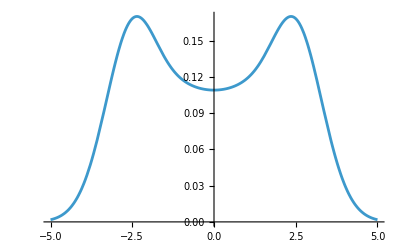

```mathematica
Plot[xMarginal,{x,-5,5}]
```

Attempting to compute ⟨ x^2 ⟩:

```mathematica
Integrate[x^2 xMarginal,{x,-∞,∞}]
```

5

We see is not correct and it differs from the exact value, only Wigner gives correct marginals to compute average values:

```mathematica
"Scalar"//SuperDagger[ψ]@((√2 QuadratureOperators[][[1]])^2)@ψ
```

9/2

The Husimi-Q function of a coherent state is also a gaussian, also for any state 0< Q(α)<=1/π and that upper bound is attained for coherent states

Let’s try with a coherent state with α = 0.5 + 0.5 ⅈ:

```mathematica
ψ = CoherentState[][0.5+0.5ⅈ]["Normalize"];
```

Get the symbolic function:

```mathematica
husimipure=Chop[husimi[(x+ⅈ p)/(√2),ψ]];
```

We verify it has a gaussian shape:

```mathematica
Plot3D[husimipure,{x,-4,4},{p,-4,4},]
```

-Graphics3D-

Upper bound numerical verification:

```mathematica
Chop[NMaximize[husimipure,{x,p}][[1]]-1/π]
```

0

Husimi-Q function of a superposition of Fock states presents interesting geometric symmetrical shapes. The patterns depend on the difference of number states values:

“Number hopping” state (try changing the number 5 to something else):

```mathematica
ψ = Sum[FockState[i],{i,2,$FockSize,5}]["Normalize"]
```

1/(√3)2+1/(√3)7+1/(√3)12

We follow the same method:

```mathematica
husimipure = husimi[(x+ⅈ p)/(√2),ψ];
```

Visualize the density plot:

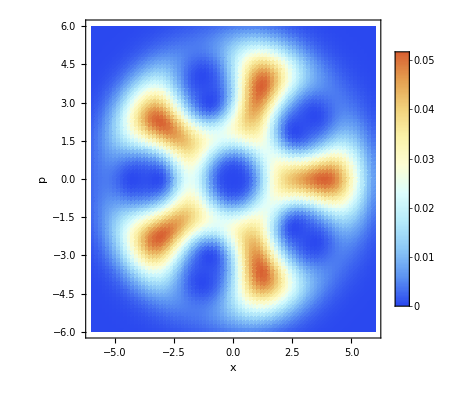

```mathematica
DensityPlot[husimipure,{x,-6,6},{p,-6,6},]
```

This definition looks apparently perfect for computational exploration, however, when the truncation size is bigger or the density matrix is heavily occupied performance issues can start to appear. In the QuantumFramework we have HusimiQRepresentation  which is adequate for any state

Set the truncation size to 50:

```mathematica
SetFockSpaceSize[50];
```

Shorthand notation for normalized coherent states:

```mathematica
coherent := CoherentState[]["Normalize"]
```

Define a statistical mixture of coherent states:

```mathematica
ψ = 2/3 coherent[2.5]["Operator"]+1/3 coherent[-2.5]["Operator"];
```

Implement the Husimi-Q definition for mixed states:

```mathematica
husimimixed =1/π Exp[-Abs[α]^2](SuperDagger[CoherentState[][α]]@ψ@CoherentState[][α])["Scalar"]/. α->(x+ⅈ p)/(√2);
```

Plot the results:

```mathematica
Plot3D[1/2Re@husimimixed,{x,-8,8},{p,-8,8},PlotRange->All,PlotPoints->100]//AbsoluteTiming
```

{4.12015,-Graphics3D-}

Same state as before but as a QuantumState:

```mathematica
ψ2 =2/3coherent[2.5]["MatrixState"]+1/3coherent[-2.5]["MatrixState"];
```

Compute the Husimi-Q function in a rectangular phase space region:

```mathematica
husi =HusimiQRepresentation[ψ2,{-8,8},{-8,8}];
```

Plot the result:

```mathematica
Plot3D[husi[x,p],{x,-8,8},{p,-8,8},PlotRange->All,PlotPoints->100]//AbsoluteTiming
```

{0.458147,-Graphics3D-}

### Connection between quasi-probability distributions

By gaussian filtering(smoothing) it is possible to go from the Wigner function to the Husimi-Q function

```mathematica
SetFockSpaceSize[20];
```

Get the phase space representations for state |2⟩:

```mathematica
wig = WignerRepresentation[FockState[2],{-4,4},{-4,4}];
```

```mathematica
husi = HusimiQRepresentation[FockState[2],{-4,4},{-4,4}];
```

Numerical integration:

```mathematica
Q[xα_,pα_]:= 2/π NIntegrate[wig[x,p] ⅇ^(-(x-xα)^2)ⅇ^(-(p-pα)^2),{x,-4,4},{p,-4,4},Method->"LocalAdaptive"]
```

Sample random points in the region:

```mathematica
diff =Abs[husi[#1,#2]-Q[#1,#2]]& @@@RandomReal[{-4,4},{50,2}];
```

Plot the absolute error:

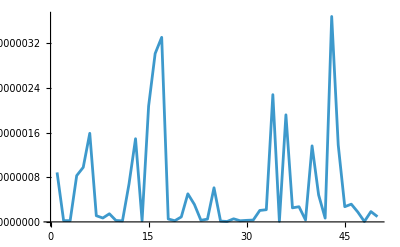

```mathematica
ListLinePlot[diff,PlotRange->All]
```

Symbolic Wigner function for state |3⟩ :

```mathematica
symbolicwig =ComplexExpand[wignerTrace["DensityMatrix"//FockState[3],α]/.{α->(x'+ⅈ p')/(√2)}]
```

-(2 ⅇ^(-(p')^2-(x')^2))/π+(12 ⅇ^(-(p')^2-(x')^2) (p')^2)/π-(12 ⅇ^(-(p')^2-(x')^2) (p')^4)/π+(8 ⅇ^(-(p')^2-(x')^2) (p')^6)/(3 π)+(12 ⅇ^(-(p')^2-(x')^2) (x')^2)/π-(24 ⅇ^(-(p')^2-(x')^2) (p')^2 (x')^2)/π+(8 ⅇ^(-(p')^2-(x')^2) (p')^4 (x')^2)/π-(12 ⅇ^(-(p')^2-(x')^2) (x')^4)/π+(8 ⅇ^(-(p')^2-(x')^2) (p')^2 (x')^4)/π+(8 ⅇ^(-(p')^2-(x')^2) (x')^6)/(3 π)

Performing the gaussian filtering integral:

```mathematica
gaussianSmoothed =1/π Integrate[symbolicwig ⅇ^(-(x'-x)^2-(p'-p)^2),{x',-∞,∞},{p',-∞,∞}]
```

(ⅇ^(-p^2/2-x^2/2) (p^2+x^2)^3)/(48 π)

We indeed recover the Husimi Q function of the state |3⟩:

```mathematica
Plot3D[gaussianSmoothed,{x,-5,5},{p,-5,5},PlotPoints->60]
```

-Graphics3D-

### S-parameter quasi-probability function and the P function limit

λ parameter displacement operator matrix (this definition works for automatic resizing of the Fock space):

```mathematica
dispmat :=Evaluate[DisplacementOperator[u+v ⅈ, "Ordering"->"Normal"]["Matrix"]];
```

Considered state:

```mathematica
ρ = FockState[4]["DensityMatrix"];
```

Characteristic function as a trace:

```mathematica
sCharacteristic[ρ_SparseArray, s_]:= ⅇ^((s Abs[u + v ⅈ]^2)/2)With[{pos = ρ["ExplicitPositions"], vals= ρ["ExplicitValues"]}, Dot[vals, dispmat[[#2,#1]]& @@@ pos]]
```

Get symbolic functions varying the s parameter(this takes a really long time because the integrals are symbolically heavy):

```mathematica
funcs =Table[complexIntegrand =FullSimplify[Exp[α (u - v ⅈ)-(u+ v ⅈ) Conjugate[α]]sCharacteristic[ρ,s],Element[{u,v},Reals]];1/π^2 Integrate[complexIntegrand,{u,-∞,∞},{v,-∞,∞}] /.α->(x+ⅈ p)/(√2),{s,0,0.9,0.1}];
```

Plot each function:

```mathematica
plots =Table[Plot3D[Evaluate[Re@funcs[[i]]],{x,-4,4},{p,-4,4},],{i,9}];
```

Show the results:

```mathematica
GraphicsGrid@Partition[Rasterize[#,RasterSize->1500]&/@plots,{3}]
```

Approaching the Glauber-Sudarshan P function limit s->1, we see the function gets progressively more singular according to the theory:

```mathematica
Plot3D[Evaluate@Re@funcs[[10]],{x,-4,4},{p,-4,4},]
```

-Graphics3D-

It also has negative values(similar to Wigner), indication of non-classical behavior as expected for a Fock state:

```mathematica
NMinimize[Re@funcs[[10]],{x,p}][[1]]
```

-14108.

Is there also an efficient numerical implementation of the s-parameter quasi-probability distribution?

We currently do not have one in the QuantumFramework, since in practice is not used too often. Of course, it is strong analytical tool that unifies all quasi-probability distributions.

Vocabulary

HusimiQRepresentation[ψ,{x_min, x_max},{p_min, p_max}] |   | Numerical representation of the Husimi-
Q function in a rectangular phase space 
region
WignerRepresentation[ψ,{x_min, x_max},{p_min, p_max}] |   | Numerical representation of the Wigner 
function in a rectangular phase space 
region